```mathematica
grMerc = Import["/home/dk0r/git/comp-phys/HW_3/position.GR_Mercury.csv"];
```

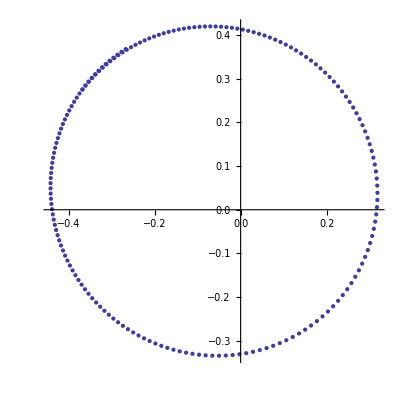

```mathematica
grMercPlot = ListPlot[grMerc, AspectRatio->Automatic]
```

```mathematica
a1= Import["/home/dk0r/git/comp-phys/HW_3/test/1.csv"];
a200= Import["/home/dk0r/git/comp-phys/HW_3/test/200.csv"];
a400= Import["/home/dk0r/git/comp-phys/HW_3/test/400.csv"];
a600= Import["/home/dk0r/git/comp-phys/HW_3/test/600.csv"];
a800= Import["/home/dk0r/git/comp-phys/HW_3/test/800.csv"];
a1000= Import["/home/dk0r/git/comp-phys/HW_3/test/1000.csv"];
a1200= Import["/home/dk0r/git/comp-phys/HW_3/test/1200.csv"];
a1400= Import["/home/dk0r/git/comp-phys/HW_3/test/1400.csv"];
a1600= Import["/home/dk0r/git/comp-phys/HW_3/test/1600.csv"];
```

Import::nffil: File not found during Import.

```mathematica
plot1= ListPlot[a1, AspectRatio->Automatic,PlotStyle->Red];
plot200= ListPlot[a200, AspectRatio->Automatic,PlotStyle->Orange];
plot400= ListPlot[a400, AspectRatio->Automatic,PlotStyle->Green];
plot600= ListPlot[a600, AspectRatio->Automatic,PlotStyle->Blue];
plot800= ListPlot[a800, AspectRatio->Automatic];
plot1000= ListPlot[a1000, AspectRatio->Automatic,PlotStyle->Purple];
plot1200= ListPlot[a1200, AspectRatio->Automatic,PlotStyle->Magenta];
plot1400= ListPlot[a1400, AspectRatio->Automatic,PlotStyle->Cyan];
plot1600= ListPlot[a1600, AspectRatio->Automatic, PlotStyle->Yellow];
```

```mathematica
Show[plot1,plot200,plot400,plot600,plot800,plot1000,plot1200,plot1400,plot1600,PlotRange->{{-0.5,0.5},{0.5,-0.5}}, Frame->True]
```

Show::gcomb: Could not combine the graphics objects in Show[plot1, plot200, plot400, plot600, plot800, plot1000, plot1200, plot1400, plot1600, PlotRange → {{-0.5, 0.5}, {0.5, -0.5}}, Frame → True].

Show[plot1,plot200,plot400,plot600,plot800,plot1000,plot1200,plot1400,plot1600,PlotRange→{{-0.5,0.5},{0.5,-0.5}},Frame→True]

```mathematica
Show[plot1,plot200,plot400,plot600,PlotRange->{{-0.5,0.5},{0.5,-0.5}},Frame->True,FrameLabel->{"Astronomical Units(au","Astronmical Units"}]
```

Show::gcomb: Could not combine the graphics objects in Show[plot1, plot200, plot400, plot600, PlotRange → {{-0.5, 0.5}, {0.5, -0.5}}, Frame → True, FrameLabel → {"Astronomical Units(au", "Astronmical Units"}].

Show[plot1,plot200,plot400,plot600,PlotRange→{{-0.5,0.5},{0.5,-0.5}},Frame→True,FrameLabel→{Astronomical Units(au,Astronmical Units}]

```mathematica
{{a1 = Import["/home/dk0r/git/comp-phys/HW_3/test/1.csv"];
a200 = Import["/home/dk0r/git/comp-phys/HW_3/test/200.csv"];
a400 = Import["/home/dk0r/git/comp-phys/HW_3/test/400.csv"];}, {a600 = Import["/home/dk0r/git/comp-phys/HW_3/test/600.csv"];}}
```

```mathematica
ListPlot[atest]
```

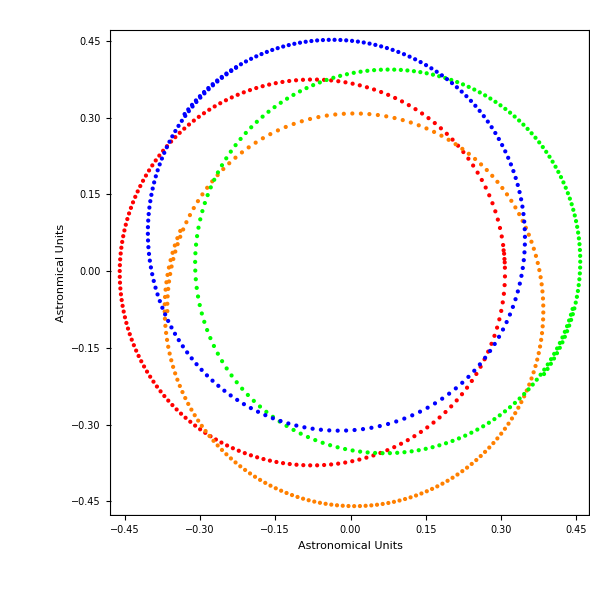

```mathematica
atest = Import["/home/dk0r/git/comp-phys/HW_3/40.csv"];
```

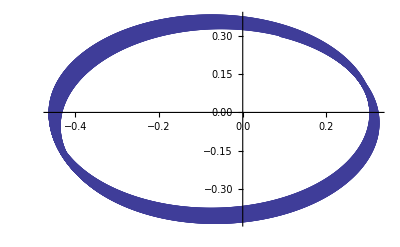

```mathematica
ListPlot[atest]
```